## Defining Functions

```mathematica
(*Preliminary functions*)

(*function convert from 2-body frame to 3-body frame*)
threebody[m1_,m2_,m3_,Rin_,Rout_,Pin_,Pout_]:=Module[{r1,r2,r3,p1,p2,p3},
r1=m2/(m1+m2)*Rin-m3/(m1+m2+m3)*Rout;
r2=-m1/(m1+m2)*Rin-m3/(m1+m2+m3)*Rout;
r3=(m1+m2)/(m1+m2+m3)*Rout;
p1=Pin-m1/(m1+m2)*Pout;
p2=-Pin-m2/(m1+m2)*Pout;
p3=Pout;
Return[Flatten[{r1,p1,r2,p2,r3,p3}]]
]


(*below is a function that converts spherical coordinate positions and velocities to cartesian coordinates*)
sphtocar[{rv_,θv_,ϕv_,rdotv_,θdotv_,ϕdotv_}]:=Module[{X,Y,Z,Xdot,Ydot,Zdot,sub,r,θ,ϕ,x,y,z,t},
sub={r[t]->rv,θ[t]->θv,ϕ[t]->ϕv,r'[t]->rdotv,θ'[t]->θdotv,ϕ'[t]->ϕdotv};
x=r[t]*Cos[ϕ[t]]*Sin[θ[t]];
y=r[t]*Sin[ϕ[t]]*Sin[θ[t]];
z=r[t]*Cos[θ[t]];
X=x/.sub;
Y=y/.sub;
Z=z/.sub;
Xdot=(D[x,t])/.sub;
Ydot=(D[y,t])/.sub;
Zdot=(D[z,t])/.sub;
Return[{X,Y,Z,Xdot,Ydot,Zdot}];
]

(*The Function Below Converts from orbital elements to cartesian coordinates*)
convertcar[{m1v_,m2v_,av_,ev_,iv_,ωv_,Ωv_,Mv_,uguessv_}]:=Module[{μ,a,e,i,ω,Ω,M,uguess,u,f,sol,r,gr,gθ,gϕ,X,Y,Z,Xdot,Ydot,fdot,Zdot,init,ϕ,θ,Mtot,rdot,θdot,ϕdot,G,ut,m1,m2,ms,au},
m1=m1v;
m2=m2v;
(*convert the masses from solar masses to kg*)
(*Mass of the sun in kg*)
(*au in meters*)

μ=m1*m2/(m1+m2);
Mtot=m1+m2;
G=6.674*10^(-11);
(*converting from au to meters*)
a=av;
e=ev;
i=iv*Pi/180;
ω=ωv*Pi/180;
Ω=Ωv*Pi/180;
M=Mv*Pi/180;
uguess=uguessv;
(*solving for eccentricity anomaly*)
sol=FindRoot[M==ut-e*Sin[ut],{ut,uguess}];
u=ut/.sol;
(*converting to the true anomaly*)
f=ArcTan[Sin[u]*Sqrt[1-e^2]/(Cos[u]-e)];
r=a*(1-e^2)/(1-e*Cos[f]);
ϕ=Ω+ArcTan[Tan[ω+f]*Cos[i]];
θ=ArcCos[Sin[ω+f]*Sin[i]];
gr=a*(1-e^2)*e*Sin[f]/((1+e*Cos[f])^2);
gθ=-1/Sin[θ]*Cos[ω+f]*Sin[i];
gϕ=(Cos[ϕ-Ω]^2)*Cos[i]/(Cos[ω+f]^2);
fdot=Sqrt[G*Mtot*(2/r-1/a)*1/(gr^2+(r*gθ)^2+(r*Sin[θ]*gϕ)^2)];
rdot=gr*fdot;
θdot=gθ*fdot;
ϕdot=gϕ*fdot;
init=sphtocar[{r,θ,ϕ,rdot,θdot,ϕdot}];
Return[init]
]

(*The function below sets default parameter values *)
(*Default parameters are the ICL PNN as defined in "Post-Newtonian Kozai–Lidov mechanism and its effect on cumulative shift
of periastron time of binary pulsar"*)
defaultpars:=Module[{assign,assignbool,assignstring,assignvec},
assign[a_,b_]:=If[NumericQ[a],0,a=b];
assignvec[a_,b_]:=If[Length[a]==0,a=b,0];
dain=0.01;
assign[ain,dain];
dein=0.01;
assign[ein,dein];
diin=60;
assign[iin,diin];
dωin=60;
assign[ωin,dωin];
dmin=0;
assign[min,dmin];
dΩin=0;
assign[Ωin,dΩin];
(*Setting Outer Orbit default values*)
daout=0.2;
assign[aout,daout];
deout=0.0;
assign[eout,deout];
diout=0;
assign[iout,diout];
dωout=0;
assign[ωout,dωout];
dmout=20;
assign[mout,dmout];
dΩout=0;
assign[Ωout,dΩout];
(*Default masses*)
dm1=1.4;
assign[m1,dm1];
dm2=1.4;
assign[m2,dm2];
dm3=1.4;
assign[m3,dm3];
(*Default guess for the eccentric anamoly. Anything on the order of 1 works well.*)
duguess=1;
assign[uguess,duguess];
(*Units are used where G,c, are given by the values given below and choose what ,mass to make 1 (from kg, default is units where solar mass is one)*)
G=6.674*10^(-11);
c=3*10^8;
ms=1.989*10^30;
dG0=1/(G);
assign[G0,dG0];
dc0=1/(c);
assign[c0,dc0];
dM0=1/(ms);
assign[M0,dM0];
(*The default for the spin is zero spin. Spin should be inputed in units where 1 denotes maximal spin*)
ds1={0,0,0};
assignvec[s1,ds1];
ds2={0,0,0};
assignvec[s2,ds2];
ds3={0,0,0};
assignvec[s3,ds3];
(*final time of integration in years for the purpose of giving it in integration units*)
dtf=10;
assign[tf,dtf];

]
(*below is a function for scaling units, y contains the positions and momenta in SI units. The choice is made to scale mass, G, and c and other units are
determined from these choices. Default is G=1,c=1,solar mass=1 *)
scale[y_]:=Module[{yscaled,ms,R0,P0,T0},
(*Defining scaling factors for position, time and momentum in terms of G0,M0,c0*)
(*scaling factors are defined such that R_my_units=R0*R_SI_units*)
R0=M0*G0/(c0^2);
T0=M0*G0/(c0^3);
P0=M0*c0;
(*scaling positions and momenta*)
yscaled=y;
yscaled[[1;;3]]=R0*y[[1;;3]];
yscaled[[7;;9]]=R0*y[[7;;9]];
yscaled[[13;;15]]=R0*y[[13;;15]];
yscaled[[4;;6]]=P0*y[[4;;6]];
yscaled[[10;;12]]=P0*y[[10;;12]];
yscaled[[16;;18]]=P0*y[[16;;18]];
(*Now scale the masses*)
m1=M0*m1;
m2=M0*m2;
m3=M0*m3;
(*Now to scale the spin. This is done by dividing by the scaled mass^2*)
s1=s1/(m1^2);
s2=s2/(m2^2);
s3=s3/(m3^2);
(*Append the scaled initial spins to the initial conditions*)
AppendTo[yscaled,Flatten[{s1,s2,s3}]];
Return[Flatten[yscaled]];
]


(*This function finally generates the initial conditions*)
initialconditions:=Module[{inner,outer,Rin,Rout,Pin,Pout,y0,yscaled,τ,T0,au},
defaultpars;
ms=1.989*10^30;
(*converting the masses from solar mass to si units*)
m1=m1*ms;
m2=m2*ms;
m3=m3*ms;
(*converting ain and aout from au to meters*)
au=1.496*10^(11);
ain=au*ain;
aout=au*aout;
inner=convertcar[{m1,m2,ain,ein,iin,ωin,Ωin,min,uguess}];
outer=convertcar[{m1+m2,m3,aout,eout,iout,ωout,Ωout,mout,uguess}];
Rin=inner[[1;;3]];
Rout=outer[[1;;3]];
Pin=m1*m2/(m1+m2)*inner[[4;;6]];
Pout=(m1+m2)*m3/(m1+m2+m3)*outer[[4;;6]];
y0=threebody[m1,m2,m3,Rin,Rout,Pin,Pout];
yscaled=scale[y0];
τ=365.25*24*3600*tf;
T0=M0*G0/(c0^3);
(*converting to scaled units*)
τ=τ*T0;
Print["t=",tf," years is"," t=",τ];
Print["y=",yscaled];
Clear@@DeleteCases[Names@"`*","sphtocar"|"defaultpars"|"scale"|"threebody"|"print"|"help"|"convertcar"|"initialconditions"|"scaleback"|"import"];
]
(*Scales back from my units to SI units*)
scaleback[r10_,r20_,r30_,p10_,p20_,p30_]:= Module[{yscaled,R0,P0,T0,au,ms,r1,r2,r3,p1,p2,p3},
defaultpars;
(*Defining scaling factors for position, time and momentum in terms of G0,M0,c0*)
(*scaling factors are defined such that R_my_units=R0*R_SI_units*)
R0=M0*G0/(c0^2);
T0=M0*G0/(c0^3);
P0=M0*c0;
(*converting back to SI units*)

r1=r10/R0;
r2=r20/R0;
r3=r30/R0;
p1=p10/P0;
p2=p20/P0;
p3=p30/P0;
Return[{r1,r2,r3,p1,p2,p3}]
]
(*code for converting from the three body frame to two one body problems *)
onebody[r1_,r2_,r3_,p1_,p2_,p3_]:=Module[{Rin,Rout,Vin,Vout},

Rin=r1-r2;
Rout=r3-(m1*r1+m2*r2)/(m1+m2);
Vin=p1/m1-p2/m2;
Vout=p3/m3-(p1+p2)/(m1+m2);
Return[{Rin, Rout,Vin,Vout}]
]
(*below is a function that converts from cartesian one body cordinates to orbital elements*)
cartokep[R_,V_,mtot_]:=Module[{En,a,i,e,Ω,n,f,θ,ω},
G=6.674*10^(-11);
(*En is the orbital energy per mass in newtonian physics*)
En=Table[1/2*V[[i]].V[[i]]-G*mtot/Norm[R[[i]]],{i,1,Length[R]}];
a=Table[-G*mtot/(2*En[[i]]),{i,1,Length[R]}];
i=Table[ArcCos[(Cross[R[[i]],V[[i]]][[3]])/Norm[Cross[R[[i]],V[[i]]]]],{i,1,Length[R]}];
e=Table[Sqrt[1-(Norm[Cross[R[[i]],V[[i]]]]^2)/(a[[i]]*G*mtot)],{i,1,Length[R]}];
n={0,0,1};
Ω=Table[If[Cross[n,Cross[R[[i]],V[[i]]]][[1]]==0,0.0,
ArcCos[(Cross[n,Cross[R[[i]],V[[i]]]].{1,0,0})/Norm[Cross[n,Cross[R[[i]],V[[i]]]]]]],{i,1,Length[R]}];
f=Table[ArcCos[(a[[i]]*(1-e[[i]]^2)-Norm[R[[i]]])/(e[[i]]*Norm[R[[i]]])],{i,1,Length[R]}];
θ=Table[ArcCos[(R[[i]][[1]]*Cos[Ω[[i]]]+R[[i]][[2]]*Sin[Ω[[i]]])/Norm[R[[i]]]],{i,1,Length[R]}];
ω=θ-f;
Return[{e,i,θ,Ω}]
]


sample[listv_,nv_]:=Module[{n,dn,listfinal},
n=nv;
dn=Floor[Length[listv]/n];
listfinal=Table[listv[[i]],{i,1,Length[listv],dn}];
Return[listfinal];
]

norm[list_]:=Module[{listfinal,x,y,z},
x=Transpose[list][[1]];
y=Transpose[list][[2]];
z=Transpose[list][[3]];

listfinal=Table[Sqrt[x[[i]]^2+y[[i]]^2+z[[i]]^2],{i,1,Length[list]}];
Return[listfinal];
]


plot[namesol_,nametime_]:=Module[{},
tf=30;
(*Importing the Data*)
SetDirectory[NotebookDirectory[]];
y=ReadList[namesol,Number];
t=ReadList[nametime,Number];
n=Length[t];
r1=Transpose[{y[[1;;n]],y[[n+1;;2*n]],y[[2*n+1;;3*n]]}];
p1=Transpose[{y[[3*n+1;;4*n]],y[[4*n+1;;5*n]],y[[5*n+1;;6*n]]}];
r2=Transpose[{y[[6*n+1;;7*n]],y[[7*n+1;;8*n]],y[[8*n+1;;9*n]]}];
p2=Transpose[{y[[9*n+1;;10*n]],y[[10*n+1;;11*n]],y[[11*n+1;;12*n]]}];
r3=Transpose[{y[[12*n+1;;13*n]],y[[13*n+1;;14*n]],y[[14*n+1;;15*n]]}];
p3=Transpose[{y[[15*n+1;;16*n]],y[[16*n+1;;17*n]],y[[17*n+1;;18*n]]}];
s1=Transpose[{y[[18*n+1;;19*n]],y[[19*n+1;;20*n]],y[[20*n+1;;21*n]]}];
s2=Transpose[{y[[21*n+1;;22*n]],y[[22*n+1;;23*n]],y[[23*n+1;;24*n]]}];
s3=Transpose[{y[[24*n+1;;25*n]],y[[25*n+1;;26*n]],y[[26*n+1;;27*n]]}];

defaultpars;
ms=1.989*10^30;
(*converting the masses from solar mass to si units*)
m1=m1*ms;
m2=m2*ms;
m3=m3*ms;
{r1f,r2f,r3f,p1f,p2f,p3f}=scaleback[r1,r2,r3,p1,p2,p3];
{Rin,Rout,Vin,Vout}=onebody[r1f,r2f,r3f,p1f,p2f,p3f];
nsample=1000; (*used to get smaller subset of points to plot*)
auf=9.859318181818183*10^(-9) (*converts distances to au*);
R0=1/0.0006779872457039338; (*Converts distances to meters*)
P0=(3.4086839904672385*10^-34)^(-1);
Rins=sample[Rin,nsample];
Vins=sample[Vin,nsample];
Routs=sample[Rout,nsample];
Vouts=sample[Vout,nsample];
time=Table[i,{i,0,tf,tf/(nsample)}]//N;
{ein,iin,θin,Ωin}=cartokep[Rins,Vins,m1+m2];
{eout,iout,θout,Ωout}=cartokep[Routs,Vouts,m1+m2+m3];

axesize=.3*inch;
ticksize=15;
Print[ListPlot[Transpose[{time,ein}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","ein"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[norm[s1],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[Transpose[s1][[1]],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1x"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[Transpose[s1][[2]],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1y"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[Transpose[s1][[3]],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1z"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[norm[s2],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s2"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[norm[s3],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s3"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,norm[Rins]*auf}],Joined->True,PlotStyle->Blue,Frame->True,FrameLabel->{"Time [earth years]","Rin [au]"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,norm[Routs]*auf}],Joined->True,PlotStyle->Blue,Frame->True,FrameLabel->{"Time [earth years]","Rout [au]"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
(*Total Orbital Angular Momentum*)
(*Lorb=Table[Cross[sample[r1,nsample][[i]]*R0,sample[p1,nsample][[i]]]*P0,{i,1,Length[time]}]+Table[Cross[sample[r2,nsample][[i]]*R0,sample[p2,nsample][[i]]]*P0,{i,1,Length[time]}]+Table[Cross[sample[r3,nsample][[i]]*R0,sample[p3,nsample][[i]]]*P0,{i,1,Length[time]}];
Print[ListPlot[Transpose[{time,norm[Lorb]}],Joined->True,PlotStyle->Blue,Frame->True,FrameLabel->{"Time [earth years]","L orbital total magnitude [kg m^2/s]"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];*)
]
```

## PNN

### ICL

#### PN1 no spin

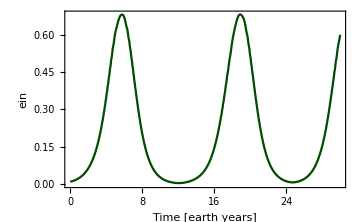

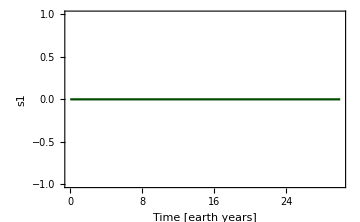

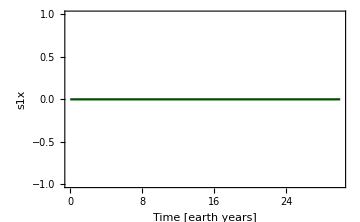

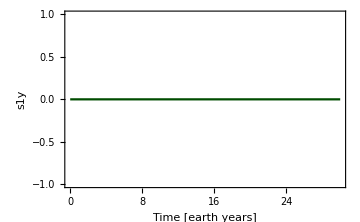

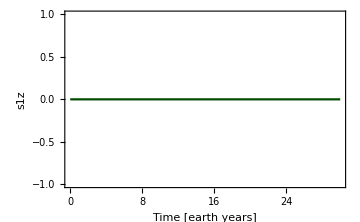

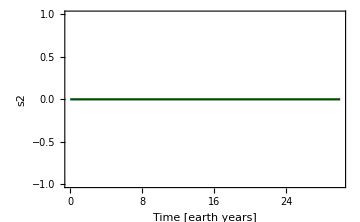

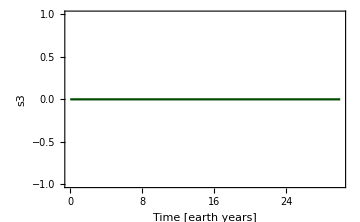

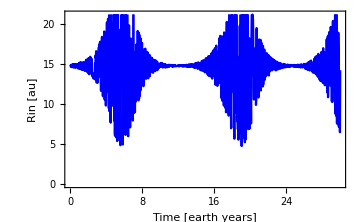

```mathematica
(*This plot corresponds to direct simulation figure 7 in "Post-Newtonian Kozai–Lidov mechanism and its effect on cumulative shift
of periastron time of binary pulsar" *)
plot["pnk1test.txt","pnk1time.txt"]
```

#### PN1 s1={0,0,1} other spins 0

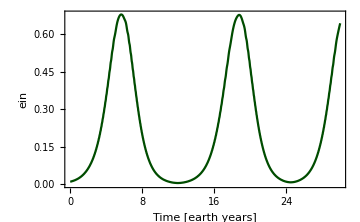

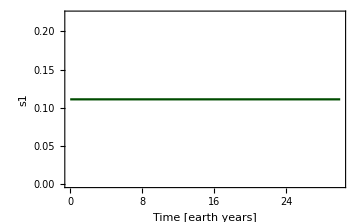

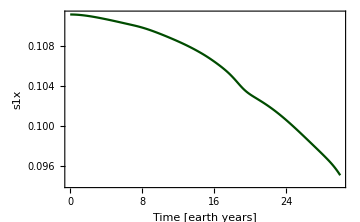

-Graphics-

-Graphics-

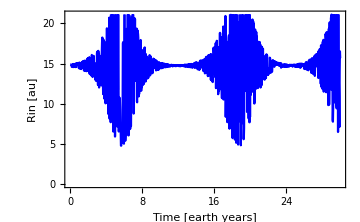

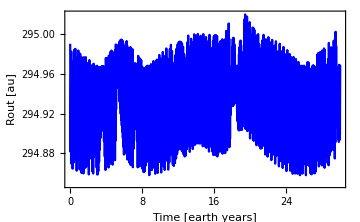

```mathematica
plot["pnk2test.txt","pnk2time.txt"]
```

#### PN1 s1={1,0,0}, s2={-1,0,0}, s3={0,0,0}

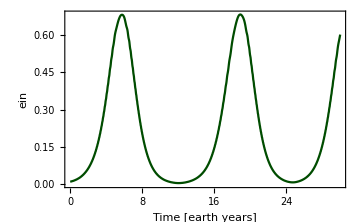

-Graphics-

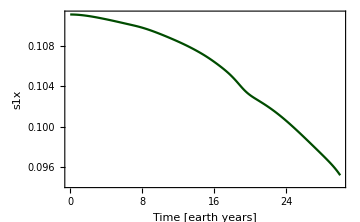

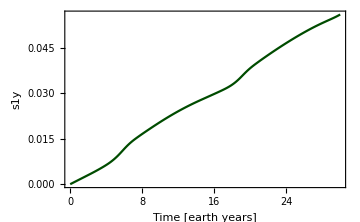

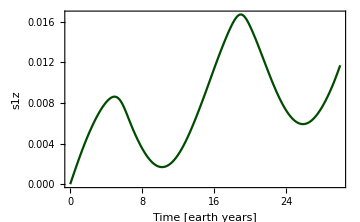

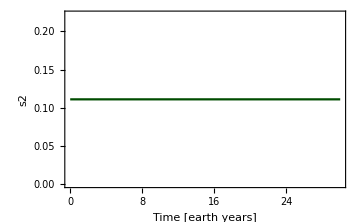

-Graphics-

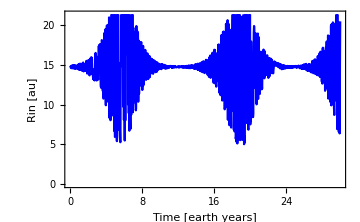

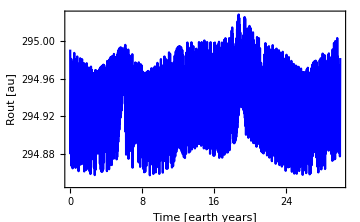

```mathematica
plot["pnk3test.txt","pnk3time.txt"]
```

#### PN2 s1={1,0,0}, s2={-1,0,0}, s3={0,1,0}

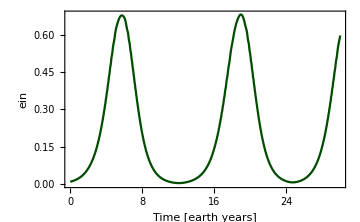

-Graphics-

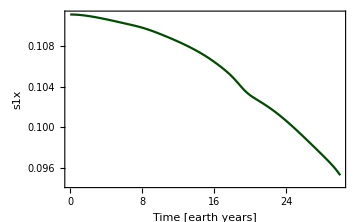

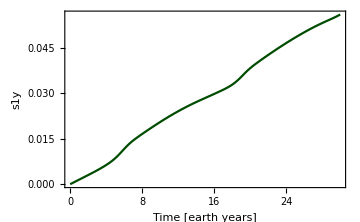

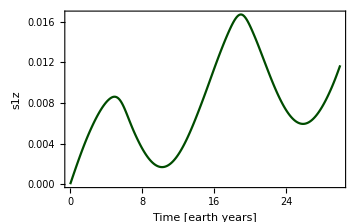

-Graphics-

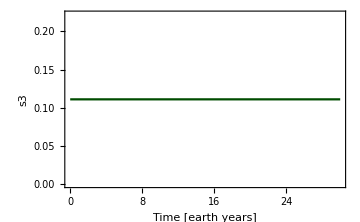

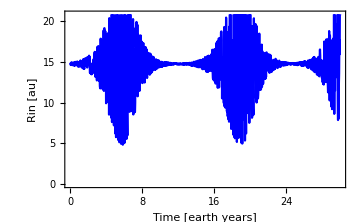

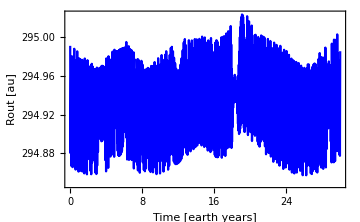

```mathematica
tf=30;
(*Importing the Data*)
SetDirectory[NotebookDirectory[]];
y=ReadList["pnk4test.txt",Number];
t=ReadList["pnk4time.txt",Number];
n=Length[t];
r1=Transpose[{y[[1;;n]],y[[n+1;;2*n]],y[[2*n+1;;3*n]]}];
p1=Transpose[{y[[3*n+1;;4*n]],y[[4*n+1;;5*n]],y[[5*n+1;;6*n]]}];
r2=Transpose[{y[[6*n+1;;7*n]],y[[7*n+1;;8*n]],y[[8*n+1;;9*n]]}];
p2=Transpose[{y[[9*n+1;;10*n]],y[[10*n+1;;11*n]],y[[11*n+1;;12*n]]}];
r3=Transpose[{y[[12*n+1;;13*n]],y[[13*n+1;;14*n]],y[[14*n+1;;15*n]]}];
p3=Transpose[{y[[15*n+1;;16*n]],y[[16*n+1;;17*n]],y[[17*n+1;;18*n]]}];
s1=Transpose[{y[[18*n+1;;19*n]],y[[19*n+1;;20*n]],y[[20*n+1;;21*n]]}];
s2=Transpose[{y[[21*n+1;;22*n]],y[[22*n+1;;23*n]],y[[23*n+1;;24*n]]}];
s3=Transpose[{y[[24*n+1;;25*n]],y[[25*n+1;;26*n]],y[[26*n+1;;27*n]]}];
(*ListPointPlot3D[r1]
ListPointPlot3D[r1-r2]*)
defaultpars
ms=1.989*10^30;
(*converting the masses from solar mass to si units*)
m1=m1*ms;
m2=m2*ms;
m3=m3*ms;
{r1f,r2f,r3f,p1f,p2f,p3f}=scaleback[r1,r2,r3,p1,p2,p3];
{Rin,Rout,Vin,Vout}=onebody[r1f,r2f,r3f,p1f,p2f,p3f];
nsample=1000; (*used to get smaller subset of points to plot*)
auf=9.859318181818183*10^(-9) (*converts distances to au*);
R0=1/0.0006779872457039338; (*Converts distances to meters*)
P0=(3.4086839904672385*10^-34)^(-1);
Rins=sample[Rin,nsample];
Vins=sample[Vin,nsample];
Routs=sample[Rout,nsample];
Vouts=sample[Vout,nsample];
time=Table[i,{i,0,tf,tf/(nsample+1)}]//N;
{ein,iin,θin,Ωin}=cartokep[Rins,Vins,m1+m2];
{eout,iout,θout,Ωout}=cartokep[Routs,Vouts,m1+m2+m3];

axesize=.3*inch;
ticksize=15;
Print[ListPlot[Transpose[{time,ein}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","ein"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[norm[s1],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[Transpose[s1][[1]],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1x"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[Transpose[s1][[2]],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1y"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[Transpose[s1][[3]],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1z"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[norm[s2],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s2"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[norm[s3],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s3"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,norm[Rins]*auf}],Joined->True,PlotStyle->Blue,Frame->True,FrameLabel->{"Time [earth years]","Rin [au]"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,norm[Routs]*auf}],Joined->True,PlotStyle->Blue,Frame->True,FrameLabel->{"Time [earth years]","Rout [au]"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
```

#### PN2.5 s1={1,0,0}, s2={-1,0,0}, s3={0,1,0}

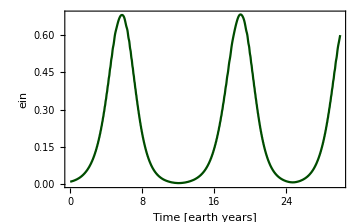

-Graphics-

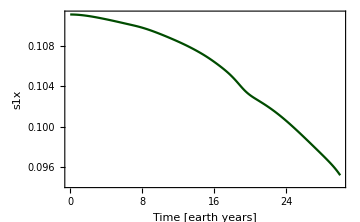

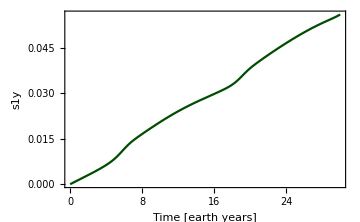

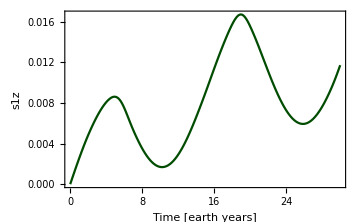

-Graphics-

-Graphics-

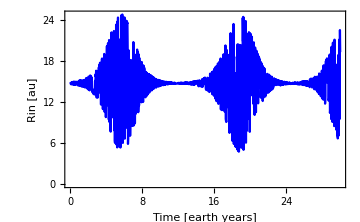

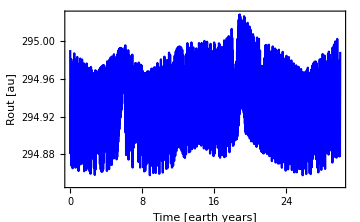

```mathematica
plot["pnk5test.txt","pnk5time.txt"]
```

#### PN2.5 s1={1,0,0}, s2={-1,0,0}, s3={0,1,0}, but tf=100 earth years (not really compiler stopped)

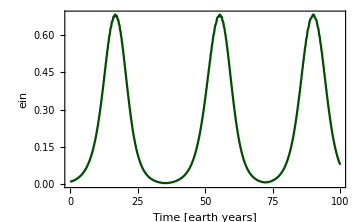

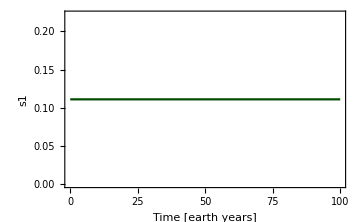

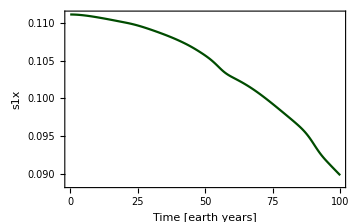

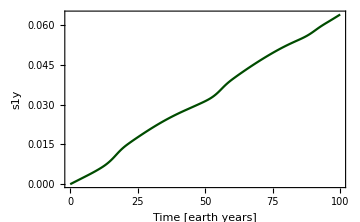

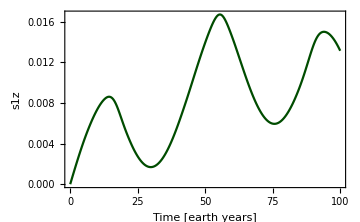

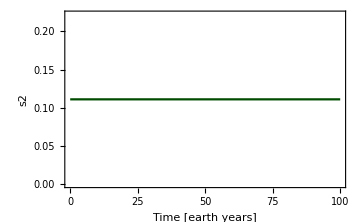

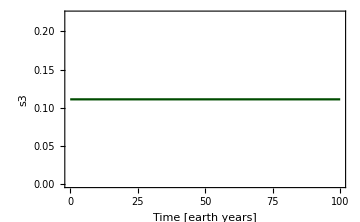

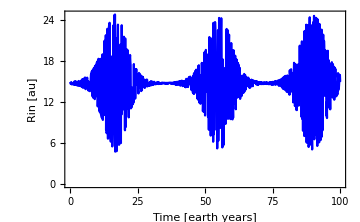

```mathematica
tf=100;
(*Importing the Data*)
SetDirectory[NotebookDirectory[]];
y=ReadList["pnk6test.txt",Number];
t=ReadList["pnk6time.txt",Number];
n=Length[t];
r1=Transpose[{y[[1;;n]],y[[n+1;;2*n]],y[[2*n+1;;3*n]]}];
p1=Transpose[{y[[3*n+1;;4*n]],y[[4*n+1;;5*n]],y[[5*n+1;;6*n]]}];
r2=Transpose[{y[[6*n+1;;7*n]],y[[7*n+1;;8*n]],y[[8*n+1;;9*n]]}];
p2=Transpose[{y[[9*n+1;;10*n]],y[[10*n+1;;11*n]],y[[11*n+1;;12*n]]}];
r3=Transpose[{y[[12*n+1;;13*n]],y[[13*n+1;;14*n]],y[[14*n+1;;15*n]]}];
p3=Transpose[{y[[15*n+1;;16*n]],y[[16*n+1;;17*n]],y[[17*n+1;;18*n]]}];
s1=Transpose[{y[[18*n+1;;19*n]],y[[19*n+1;;20*n]],y[[20*n+1;;21*n]]}];
s2=Transpose[{y[[21*n+1;;22*n]],y[[22*n+1;;23*n]],y[[23*n+1;;24*n]]}];
s3=Transpose[{y[[24*n+1;;25*n]],y[[25*n+1;;26*n]],y[[26*n+1;;27*n]]}];
(*ListPointPlot3D[r1]
ListPointPlot3D[r1-r2]*)
defaultpars;
ms=1.989*10^30;
(*converting the masses from solar mass to si units*)
m1=m1*ms;
m2=m2*ms;
m3=m3*ms;
{r1f,r2f,r3f,p1f,p2f,p3f}=scaleback[r1,r2,r3,p1,p2,p3];
{Rin,Rout,Vin,Vout}=onebody[r1f,r2f,r3f,p1f,p2f,p3f];
nsample=1000; (*used to get smaller subset of points to plot*)
auf=9.859318181818183*10^(-9) (*converts distances to au*);
R0=1/0.0006779872457039338; (*Converts distances to meters*)
P0=(3.4086839904672385*10^-34)^(-1);
Rins=sample[Rin,nsample];
Vins=sample[Vin,nsample];
Routs=sample[Rout,nsample];
Vouts=sample[Vout,nsample];
time=Table[i,{i,0,tf,tf/(nsample+1)}]//N;
{ein,iin,θin,Ωin}=cartokep[Rins,Vins,m1+m2];
{eout,iout,θout,Ωout}=cartokep[Routs,Vouts,m1+m2+m3];

axesize=.3*inch;
ticksize=15;
Print[ListPlot[Transpose[{time,ein}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","ein"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[norm[s1],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[Transpose[s1][[1]],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1x"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[Transpose[s1][[2]],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1y"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[Transpose[s1][[3]],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s1z"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[norm[s2],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s2"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,sample[norm[s3],nsample]}],Joined->True,PlotStyle->Darker[Darker[Darker[Green]]],Frame->True,FrameLabel->{"Time [earth years]","s3"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,norm[Rins]*auf}],Joined->True,PlotStyle->Blue,Frame->True,FrameLabel->{"Time [earth years]","Rin [au]"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
Print[ListPlot[Transpose[{time,norm[Routs]*auf}],Joined->True,PlotStyle->Blue,Frame->True,FrameLabel->{"Time [earth years]","Rout [au]"},LabelStyle->Directive[Black,Bold],FrameTicksStyle->Directive[Black,ticksize],ImageSize->Medium]];
```

### IEL

#### PN1 no spin

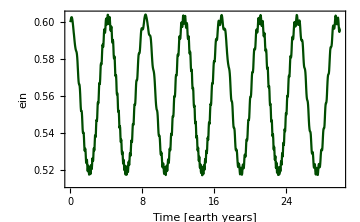

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

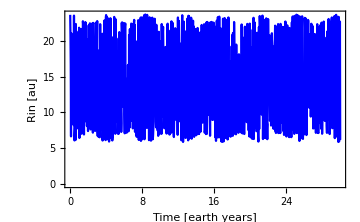

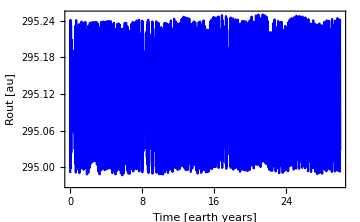

```mathematica
(*This simulation corresponds to fig 7 direct simulation in "Post-Newtonian Kozai–Lidov mechanism and its effect on cumulative shift
of periastron time of binary pulsar" except the time axis is currently off since the simulation didn't finish running all the way to 30 years*)
plot["pnk7test.txt","pnk7time.txt"]
```

#### PN2.5 s1={1,0,0}, s2={0,1,0}, s3={0,0,1}

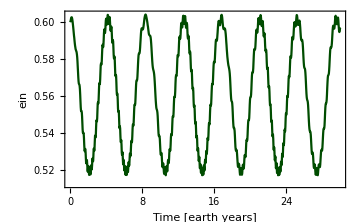

-Graphics-

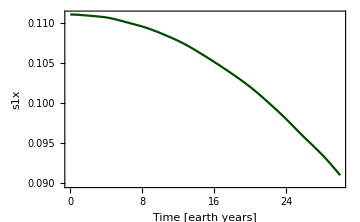

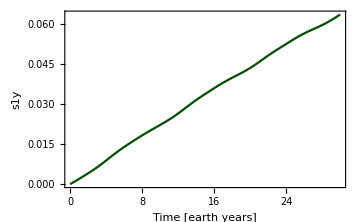

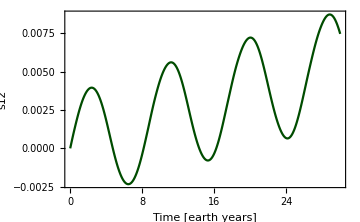

-Graphics-

-Graphics-

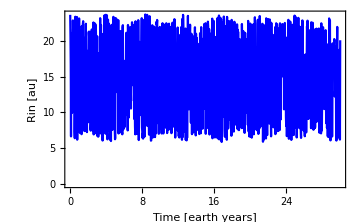

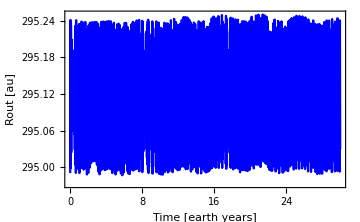

```mathematica
plot["pnk8test.txt","pnk8time.txt"]
```